```mathematica
(*Algorithm:LM-STLS (Levenberg-Marquardt Sequential Thresholded Least Squares)
Reference to cite when using this code:[1] A noise-corrected data-driven approach for nonlinear dynamical system modeling in frequency domain,2026.
Code availability:This program is open for academic research only.Unauthorized commercial redistribution is prohibited.
================================================================================*)
```

```mathematica
(*Import self-defined package for nonlinear sparse identification*)
Import["NCSINDyPackage.m","Package"]
```

```mathematica
(* ======================Basic System Configuration======================*)
(*n:nonlinear polynomial order;order:Fourier series expansion order*)
n=7;order=5;opts={AccuracyGoal->12,PrecisionGoal->12,MaxStepFraction->1/1000  };
(*Governing differential equation of nonlinear oscillator*)
Eq01={m x''[t]+c x'[t]+∑_(j1=1)^n Subscript[k, j1] x[t]^j1-F Cos[Ω t]==0};
(*Initial conditions of dynamic system*)
InitCond01={x[0]==0, x'[0]==0};
(*True physical parameter values for simulation*)
Par01=Join[{m->1,c->0.4,F->1},Thread[Table[Subscript[k, j1],{j1,1,n}]->{1,0,0.5,0,0.1,0,0}]];
(*List of undetermined physical coefficients to be identified*)
Var=Join[{m,c},Table[Subscript[k, j1],{j1,1,n}]];
```

```mathematica
(* ======================Fourier Series Model Definition======================*)
(*Displacement,velocity,acceleration Fourier series model*)
(*DispModel:displacement Fourier approximation*)
DispModel=Subscript[A, s,0]+∑_(j1=1)^order (Subscript[A, s,j1] Cos[j1 Ω t]+Subscript[B, s,j1] Sin[j1 Ω t]);
(*Coefficient list for displacement Fourier series*)
DispCoeff=Join[{Subscript[A, s,0]},Flatten[Table[{Subscript[A, s,j1],Subscript[B, s,j1]},{j1,order}]]];

(*VeloModel:velocity Fourier approximation*)
VeloModel=Subscript[A, v,0]+∑_(j1=1)^order (Subscript[A, v,j1] Cos[j1 Ω t]+Subscript[B, v,j1] Sin[j1 Ω t]);VeloCoeff=Join[{Subscript[A, v,0]},Flatten[Table[{Subscript[A, v,j1],Subscript[B, v,j1]},{j1,order}]]];
(*AcceModel:acceleration Fourier approximation*)
AcceModel=Subscript[A, a,0]+∑_(j1=1)^order (Subscript[A, a,j1] Cos[j1 Ω t]+Subscript[B, a,j1] Sin[j1 Ω t]);AcceCoeff=Join[{Subscript[A, a,0]},Flatten[Table[{Subscript[A, a,j1],Subscript[B, a,j1]},{j1,order}]]];
(*Harmonic orders used for noise correction*)
OrderCorrect={3,4,5};
(*Coefficient set of noise correction terms*)
CorrectModel=Sum[Subscript[δA, s,j1] Cos[j1 Ω t]+Subscript[δB, s,j1] Sin[j1 Ω t],{j1,OrderCorrect}];
(*Coefficient set of noise correction terms*)
CorrectCoeff=DeleteCases[Flatten[Table[{Subscript[δA, s,j1],Subscript[δB, s,j1]},{j1,OrderCorrect}]],Subscript[δB, s,0]];
(*Sub-function:construct correction coefficients for each excitation frequency*)
CorrectCoeffj[jj_]:=Join[{Subscript[δA, s,0][jj]},Flatten[Table[{Subscript[δA, s,j1][jj],Subscript[δB, s,j1][jj]},{j1,order}]]]/.Subscript[x1_, x2_,x3_][x4_]/;MemberQ[Complement[Range[0,order],OrderCorrect],x3]->0;
(*Extract variable symbols of noise correction coefficients*)
CorrectCoeffjVar[jj_]:=DeleteCases[Flatten[Table[{Subscript[δA, s,j1][jj],Subscript[δB, s,j1][jj]},{j1,OrderCorrect}]],Subscript[δB, s,0][jj]];
```

```mathematica
(*Nonlinear stiffness model library constructed from displacement harmonics*)
StiffnessModel=ModelLibFun[{DispCoeff},n,order];
(*Excitation frequency list for sweeping analysis*)
OmegaList=Range[0.4,2.8,0.4];
(*Sampling time sequence*)
TimeData=Range[800,1000,0.01];
(*Signal-to-Noise Ratio*)SNR=10;
```

```mathematica
(*Load preset noise data from external file for reproducibility*)
Noise=Transpose[Import["C:/Users/Administrator/Desktop/Noise41.xls"][[1]]];
```

```mathematica
(* ======================Generate Dynamic Response Data======================*)
For[j2=1,j2≤Length[OmegaList],j2++,
(*Solve ODE to obtain true displacement response*)
Sol01[j2]=NDSolveValue[Join[Eq01,InitCond01]/.Par01/.Ω->OmegaList[[j2]],x,{t,0,1000},opts];
(*True displacement time series data*)
DispData[j2]=Array[{TimeData[[#]],Sol01[j2][TimeData[[#]]]}&,Length[TimeData]];
DispSigTrue[j2]=Array[Sol01[j2][TimeData[[#]]]&,Length[TimeData]];
(*Add preset noise to obtain measured noisy displacement*)
(*DispSigNois[j2]=AddNoiseFun[DispSigTrue[j2],0,SNR];*)
DispSigNois[j2]=Noise[[j2]];
DispDataMeas[j2]=Array[{TimeData[[#]],DispSigTrue[j2][[#]]+DispSigNois[j2][[#]]}&,Length[TimeData]];(* ======================Fourier Coefficient Identification via Fitting======================*)(*Fourier coefficients fitted from noisy measured data*)
Ameas[x][j2]=DispCoeff/.FindFit[DispDataMeas[j2],DispModel/.Par01/.Ω->OmegaList[[j2]],DispCoeff,t];
(*Fourier coefficients fitted from noise-free true data*)
Atrue[x][j2]=DispCoeff/.FindFit[DispData[j2],DispModel/.Par01/.Ω->OmegaList[[j2]],DispCoeff,t];
(*Fourier coefficients of pure noise component*)
Anois[x][j2]=CorrectCoeff/.FindFit[Array[{TimeData[[#]],DispSigNois[j2][[#]]}&,Length[TimeData]],CorrectModel/.Par01/.Ω->OmegaList[[j2]],CorrectCoeff,t];
(*Noise correction for displacement harmonic coefficients*)
A[x][j2]=ReplacePart[Ameas[x][j2]-(CorrectCoeffj[j2]/.Ω->OmegaList[[j2]]),1->0];
(* ======================Full-State Reconstruction via SVA Transform======================*)(*Reconstruct velocity and acceleration from corrected displacement harmonics*)
A[x'][j2]=ReplacePart[SVATransform[A[x][j2],"rad/s",OmegaList[[j2]],"s2v"],1->0];
A[x''][j2]=ReplacePart[SVATransform[A[x][j2],"rad/s",OmegaList[[j2]],"s2a"],1->0];
(*Excitation force harmonic coefficients*)
A[f][j2]=Join[{0,F},Table[0,2order-1]]/.Par01;
(*Construct nonlinear library matrix in frequency domain*)
ModelLibrary[j2]=StiffnessModel/.Thread[DispCoeff->A[x][j2]];
(*Assemble Jacobian-like matrix and residual vector for nonlinear least squares*)
AA1[j2]=Join[{A[x''][j2]}ᵀ,{A[x'][j2]}ᵀ,ModelLibrary[j2],2].{Var}ᵀ//Chop;
RR1[j2]=Flatten[AA1[j2]-{A[f][j2]}ᵀ];
Print[j2];
];
```

1

2

3

4

5

6

7

```mathematica
(* ======================Prepare Training Data for Sparse Regression======================*)(*Collect noisy and noise-free training time-series data*)
TrainDataDispMeas=Table[DispDataMeas[j1],{j1,1,Length[OmegaList]}];TrainDataDispTrue=Table[DispData[j1],{j1,1,Length[OmegaList]}];
(*Plot noisy and true displacement responses*)
Fig2aNoise=ListLinePlot[Flatten[Table[DispDataMeas[j1][[All,2]],{j1,1,Length[OmegaList]}]],PlotStyle->{Red,Dotted},Frame->True];
Fig2aTrue=ListLinePlot[Flatten[Table[DispData[j1][[All,2]],{j1,1,Length[OmegaList]}]],PlotStyle->{Blue},Frame->True];
Fig2a=Show[Fig2aNoise,Fig2aTrue,PlotRange->{-3,3}]
```

-Graphics-

```mathematica
(*Combine residual across all excitation frequencies*)
Residual=Join@@Table[RR1[j2],{j2,1,Length[OmegaList]}];
(*Merge physical parameters and noise correction coefficients into full variable set*)
Variable=Join[Var,Table[Join[CorrectCoeffjVar[j2]],{j2,1,Length[OmegaList]}]//Flatten];
(*Compute Jacobian matrix of residual with respect to unknown variables*)
JacobiFun=D[Residual,{Variable,1}];
(* ======================LM-STLS Algorithm Hyperparameters======================*)
ConvTol=10^-6;maxLMIter=100;
Lambda=0.02;maxSparseIter=10;
(*Indices of physical terms forced to be retained during thresholding*)
InitbigIndices=Join[Range[Length[Var]+1,Length[Variable]]];
```

```mathematica
(*Initial guess of unknown parameter vector*)
InitGuess=ReplacePart[ReplacePart[0.2*Variable/.Par01,Thread[Range[Length[Var]+1,Length[Variable]]->0]],Thread[{4,6,8,9}->1]];
(*Execute proposed LM-STLS nonlinear sparse regression*)
Xi=NonLinearSparsifyDynamics[JacobiFun,Residual,Variable,InitGuess,ConvTol,maxLMIter,Lambda,maxSparseIter,InitbigIndices];
```

{1,49}

{2,47}

{3,47}

{4,47}

{5,47}

{6,47}

{7,47}

{8,47}

{9,47}

{10,47}

```mathematica
(* ======================Quantitative Evaluation Metrics======================*)
(*g1:Number of non-zero identified terms (sparsity evaluation)*)
(*g2:Relative L2 error between identified parameters and true values (accuracy evaluation)*)
g1=Table[Count[Xi[[1]][[j1,1;;9]],x_/;x≠0],{j1,1,Xi[[2]]//Total}];
g2=Table[Norm[Xi[[1]][[j1,1;;9]]-Var/.Par01]/Norm[Var/.Par01],{j1,1,Xi[[2]]//Total}];
```

```mathematica
(*Show iterative evolution of parameter identification for {m,c,Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7]}*)
Xi[[1]]//MatrixForm
```

(0.2 | 0.08 | 0.2 | 1. | 0.1 | 1. | 0.02 | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.0046 | 0.404071 | 1.02467 | 0.0105903 | 0.523401 | -0.0182603 | -0.089698 | -0.0153238 | 0.0901487 | -0.000405372 | 0.000560964 | -0.00236111 | 0.00358069 | 0.000311218 | 0.000842416 | -0.00210167 | 0.00524456 | -0.00447747 | -0.0107023 | 0.00825408 | -0.00229503 | 0.00476261 | -0.00191396 | 0.00620443 | -0.0155882 | -0.0230212 | 0.00548377 | 0.00169237 | -0.0113885 | -0.00173708 | 0.00860891 | 0.0165938 | 0.00716766 | -0.000067451 | -0.00117649 | -0.00104108 | -0.00187056 | 0.000274287 | 0.00512521 | -0.0028134 | -0.00270346 | 0.00233578 | 0.00033744 | 0.0017411 | 0.000959446 | -0.00148135 | -0.00143482 | -0.000177363 | 0.00115983 | 0.00160048 | -0.00197174
0.999149 | 0.398216 | 0.981609 | 0.028004 | 0.598715 | -0.0420162 | -0.0134595 | 0.0150053 | 0.0341201 | -0.00192157 | -0.00120505 | -0.00126646 | -0.000865859 | -0.00270876 | -0.00085084 | 0.00424488 | 0.00598695 | -0.000157388 | 0.00201312 | 0.00199124 | 0.00480453 | -0.00053265 | -0.00142175 | 0.00378177 | -0.00762409 | -0.00224413 | -0.00147206 | 0.0000419979 | -0.00221768 | -0.0000500554 | 0.00177817 | 0.00339098 | 0.00163286 | -0.000015114 | -0.000250881 | -0.000217992 | -0.0003573 | 0.0000485891 | 0.00103625 | -0.000559945 | -0.000549856 | 0.000470334 | 0.0000674663 | 0.000357217 | 0.000195065 | -0.00030238 | -0.000288194 | -0.0000361846 | 0.000232324 | 0.000325787 | -0.000399718
0.998685 | 0.399441 | 0.981211 | 0.0329784 | 0.585395 | -0.0507213 | 0.0117183 | 0.0181786 | 0.0244607 | -0.00198707 | -0.000529211 | -0.00123923 | -0.00102847 | -0.00287836 | -0.00070262 | 0.00421171 | 0.00588926 | -0.0000451569 | 0.00233266 | 0.00193656 | 0.00488428 | -0.00018046 | -0.000892091 | 0.00382719 | -0.00791251 | -0.00238485 | -0.00139036 | 0.0000131657 | -0.00216728 | -0.0000350173 | 0.00173325 | 0.00331722 | 0.00159708 | -0.0000168249 | -0.000245639 | -0.000214527 | -0.000349085 | 0.0000489618 | 0.00101473 | -0.000550565 | -0.000537874 | 0.000460863 | 0.0000652963 | 0.000350312 | 0.000190639 | -0.000297201 | -0.000281825 | -0.0000351315 | 0.000227518 | 0.000318642 | -0.000391744
0.999279 | 0.39946 | 0.986279 | 0.0334692 | 0.564629 | -0.0515886 | 0.0346498 | 0.0185089 | 0.0175483 | -0.00253986 | -0.000962916 | -0.00121172 | -0.00103515 | -0.00304377 | -0.000875014 | 0.00422207 | 0.00590774 | -0.0000431008 | 0.00233884 | 0.00193871 | 0.00482281 | -0.000188011 | -0.000866429 | 0.00382966 | -0.00791301 | -0.00239613 | -0.00139388 | 6.90209×10^-6 | -0.00213399 | -0.0000351054 | 0.00173276 | 0.00331605 | 0.00159551 | -0.0000197631 | -0.000242255 | -0.000214519 | -0.000349127 | 0.0000489692 | 0.00101468 | -0.000551233 | -0.000537346 | 0.000460861 | 0.0000652948 | 0.00035031 | 0.000190635 | -0.000297388 | -0.000281711 | -0.0000351304 | 0.000227514 | 0.00031864 | -0.00039174
0.999576 | 0.399469 | 0.988798 | 0.0335459 | 0.554413 | -0.0517255 | 0.0458642 | 0.0185612 | 0.0141822 | -0.00281279 | -0.0011772 | -0.00120026 | -0.00103993 | -0.00312596 | -0.000961398 | 0.00422954 | 0.00591897 | -0.0000430342 | 0.00233982 | 0.00193983 | 0.00479284 | -0.000191396 | -0.000854011 | 0.00383007 | -0.00791308 | -0.00240126 | -0.00139522 | 3.80025×10^-6 | -0.00211758 | -0.0000351149 | 0.00173263 | 0.00331549 | 0.00159474 | -0.0000212098 | -0.000240586 | -0.000214518 | -0.000349149 | 0.0000489742 | 0.00101465 | -0.000551564 | -0.000537088 | 0.000460862 | 0.0000652945 | 0.000350311 | 0.000190634 | -0.000297482 | -0.000281655 | -0.0000351297 | 0.000227513 | 0.00031864 | -0.00039174
0.99963 | 0.399471 | 0.989256 | 0.0335659 | 0.552549 | -0.0517625 | 0.0479149 | 0.0185755 | 0.0135659 | -0.00286406 | -0.00121386 | -0.0011958 | -0.00104139 | -0.00314132 | -0.000976723 | 0.00423073 | 0.00592087 | -0.0000429991 | 0.0023401 | 0.00194003 | 0.00478736 | -0.00019201 | -0.000851755 | 0.00383019 | -0.00791311 | -0.00240223 | -0.00139548 | 3.23454×10^-6 | -0.00211459 | -0.0000351164 | 0.00173259 | 0.00331539 | 0.0015946 | -0.0000214735 | -0.000240282 | -0.000214518 | -0.000349155 | 0.0000489752 | 0.00101465 | -0.000551624 | -0.000537041 | 0.000460863 | 0.0000652944 | 0.000350311 | 0.000190633 | -0.0002975 | -0.000281645 | -0.0000351295 | 0.000227512 | 0.00031864 | -0.00039174
0.999634 | 0.399471 | 0.989284 | 0.0335688 | 0.55243 | -0.0517679 | 0.0480471 | 0.0185775 | 0.013526 | -0.00286777 | -0.00121572 | -0.00119502 | -0.0010416 | -0.00314239 | -0.000977641 | 0.00423078 | 0.00592097 | -0.0000429908 | 0.00234014 | 0.00194004 | 0.00478701 | -0.000192048 | -0.000851614 | 0.00383021 | -0.00791311 | -0.00240229 | -0.00139549 | 3.19818×10^-6 | -0.0021144 | -0.0000351165 | 0.00173259 | 0.00331538 | 0.00159459 | -0.0000214904 | -0.000240263 | -0.000214518 | -0.000349155 | 0.0000489752 | 0.00101465 | -0.000551628 | -0.000537038 | 0.000460863 | 0.0000652944 | 0.000350311 | 0.000190633 | -0.000297501 | -0.000281644 | -0.0000351295 | 0.000227512 | 0.00031864 | -0.00039174
0.999634 | 0.399471 | 0.989285 | 0.0335689 | 0.552427 | -0.0517682 | 0.0480504 | 0.0185777 | 0.013525 | -0.0028679 | -0.00121574 | -0.00119497 | -0.00104161 | -0.00314243 | -0.00097766 | 0.00423078 | 0.00592097 | -0.0000429902 | 0.00234014 | 0.00194004 | 0.004787 | -0.000192049 | -0.000851611 | 0.00383021 | -0.00791311 | -0.00240229 | -0.0013955 | 3.19727×10^-6 | -0.0021144 | -0.0000351165 | 0.00173259 | 0.00331538 | 0.00159459 | -0.0000214908 | -0.000240262 | -0.000214518 | -0.000349155 | 0.0000489752 | 0.00101465 | -0.000551628 | -0.000537038 | 0.000460863 | 0.0000652944 | 0.000350311 | 0.000190633 | -0.000297501 | -0.000281644 | -0.0000351295 | 0.000227512 | 0.00031864 | -0.00039174
0.999634 | 0.399471 | 0.989285 | 0.0335689 | 0.552427 | -0.0517682 | 0.0480505 | 0 | 0 | -0.0028679 | -0.00121574 | -0.00119496 | -0.00104161 | -0.00314243 | -0.00097766 | 0.00423078 | 0.00592097 | -0.0000429902 | 0.00234014 | 0.00194004 | 0.004787 | -0.000192049 | -0.000851611 | 0.00383021 | -0.00791311 | -0.00240229 | -0.0013955 | 3.19725×10^-6 | -0.0021144 | -0.0000351165 | 0.00173259 | 0.00331538 | 0.00159459 | -0.0000214908 | -0.000240262 | -0.000214518 | -0.000349155 | 0.0000489752 | 0.00101465 | -0.000551628 | -0.000537038 | 0.000460863 | 0.0000652944 | 0.000350311 | 0.000190633 | -0.000297501 | -0.000281644 | -0.0000351295 | 0.000227512 | 0.00031864 | -0.00039174
0.999045 | 0.399434 | 0.988664 | 0.0119423 | 0.534732 | -0.0066543 | 0.0822974 | 0 | 0 | -0.00272371 | -0.000532031 | -0.00157392 | -0.000421627 | -0.00315608 | -0.000689547 | 0.00372844 | 0.00549252 | -0.000148572 | 0.00208225 | 0.00192883 | 0.00468953 | -0.000262031 | -0.000674107 | 0.00360306 | -0.00782418 | -0.00253807 | -0.00144824 | 1.7568×10^-6 | -0.00210739 | -0.0000309634 | 0.00175149 | 0.00331362 | 0.00159216 | -0.0000236336 | -0.000237662 | -0.000214946 | -0.000348336 | 0.0000489878 | 0.00101457 | -0.000552176 | -0.000536627 | 0.000460792 | 0.000065375 | 0.000350314 | 0.000190629 | -0.000297673 | -0.000281533 | -0.000035144 | 0.000227524 | 0.00031864 | -0.000391741
1.00023 | 0.399478 | 0.995811 | 0.0101548 | 0.519027 | -0.00547035 | 0.0896058 | 0 | 0 | -0.00347276 | -0.00137408 | -0.00170703 | -0.000415017 | -0.00335518 | -0.00109201 | 0.00408045 | 0.0058151 | -0.000160444 | 0.00205508 | 0.00193831 | 0.00467283 | -0.000221812 | -0.000765408 | 0.00362768 | -0.00783501 | -0.00246097 | -0.0014153 | -5.61279×10^-6 | -0.00206776 | -0.0000308328 | 0.00175203 | 0.00331326 | 0.00159161 | -0.0000261406 | -0.000234702 | -0.000214961 | -0.000348339 | 0.0000489906 | 0.00101456 | -0.000552723 | -0.000536209 | 0.000460791 | 0.0000653771 | 0.000350314 | 0.000190628 | -0.000297833 | -0.000281435 | -0.0000351436 | 0.000227523 | 0.000318641 | -0.000391741
1.00054 | 0.399493 | 0.997709 | 0.0101137 | 0.515026 | -0.00544493 | 0.0914328 | 0 | 0 | -0.0036841 | -0.00168994 | -0.00171414 | -0.000426194 | -0.00341054 | -0.00120962 | 0.00417376 | 0.00589706 | -0.000160444 | 0.00205462 | 0.0019412 | 0.00466979 | -0.000212654 | -0.000782883 | 0.00362823 | -0.00783556 | -0.00244156 | -0.00140688 | -7.53239×10^-6 | -0.00205763 | -0.0000308247 | 0.00175197 | 0.00331317 | 0.00159148 | -0.0000267734 | -0.000233965 | -0.000214961 | -0.00034835 | 0.0000489914 | 0.00101456 | -0.00055286 | -0.000536103 | 0.000460792 | 0.0000653771 | 0.000350314 | 0.000190628 | -0.000297872 | -0.000281411 | -0.0000351433 | 0.000227522 | 0.000318641 | -0.000391741
1.00057 | 0.399494 | 0.997876 | 0.0101097 | 0.514676 | -0.0054426 | 0.0915924 | 0 | 0 | -0.00370022 | -0.0017166 | -0.00171531 | -0.000428671 | -0.00341522 | -0.00121988 | 0.00418193 | 0.00590425 | -0.000160442 | 0.00205458 | 0.00194145 | 0.00466952 | -0.000211862 | -0.000784377 | 0.00362828 | -0.00783563 | -0.00243987 | -0.00140615 | -7.70054×10^-6 | -0.00205675 | -0.0000308228 | 0.00175196 | 0.00331316 | 0.00159147 | -0.0000268285 | -0.000233901 | -0.000214961 | -0.000348352 | 0.0000489915 | 0.00101455 | -0.000552872 | -0.000536094 | 0.000460792 | 0.0000653771 | 0.000350314 | 0.000190628 | -0.000297875 | -0.000281409 | -0.0000351432 | 0.000227522 | 0.000318641 | -0.000391741
1.00057 | 0.399494 | 0.997881 | 0.0101094 | 0.514667 | -0.00544241 | 0.0915968 | 0 | 0 | -0.00370044 | -0.00171719 | -0.00171541 | -0.000428894 | -0.00341533 | -0.00122015 | 0.00418215 | 0.00590444 | -0.000160442 | 0.00205458 | 0.00194146 | 0.00466952 | -0.000211841 | -0.000784416 | 0.00362828 | -0.00783563 | -0.00243982 | -0.00140613 | -7.70526×10^-6 | -0.00205672 | -0.0000308227 | 0.00175196 | 0.00331316 | 0.00159147 | -0.0000268301 | -0.0002339 | -0.000214961 | -0.000348352 | 0.0000489915 | 0.00101455 | -0.000552872 | -0.000536093 | 0.000460792 | 0.0000653771 | 0.000350314 | 0.000190628 | -0.000297875 | -0.000281409 | -0.0000351432 | 0.000227522 | 0.000318641 | -0.000391741
1.00057 | 0.399494 | 0.997881 | 0 | 0.514666 | 0 | 0.0915968 | 0 | 0 | -0.00370043 | -0.00171719 | -0.00171542 | -0.000428902 | -0.00341533 | -0.00122015 | 0.00418215 | 0.00590445 | -0.000160442 | 0.00205458 | 0.00194146 | 0.00466952 | -0.000211841 | -0.000784417 | 0.00362828 | -0.00783563 | -0.00243982 | -0.00140613 | -7.70531×10^-6 | -0.00205672 | -0.0000308227 | 0.00175196 | 0.00331316 | 0.00159147 | -0.0000268301 | -0.0002339 | -0.000214961 | -0.000348352 | 0.0000489915 | 0.00101455 | -0.000552872 | -0.000536093 | 0.000460792 | 0.0000653771 | 0.000350314 | 0.000190628 | -0.000297875 | -0.000281409 | -0.0000351432 | 0.000227522 | 0.000318641 | -0.000391741
1.00057 | 0.399498 | 0.997921 | 0 | 0.514612 | 0 | 0.0916136 | 0 | 0 | -0.00369792 | -0.0018271 | -0.00272218 | -0.000680815 | -0.00341788 | -0.00123939 | 0.00418406 | 0.00590725 | -0.000195573 | 0.00193758 | 0.0019411 | 0.00466956 | -0.000213863 | -0.000784356 | 0.00376044 | -0.00788168 | -0.00243953 | -0.0014066 | -7.93425×10^-6 | -0.00205615 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159145 | -0.0000268684 | -0.000233744 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552886 | -0.000536093 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297888 | -0.000281396 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997949 | 0 | 0.514553 | 0 | 0.0916401 | 0 | 0 | -0.00370023 | -0.00184214 | -0.00273221 | -0.000683626 | -0.00341893 | -0.00124185 | 0.00418545 | 0.00590848 | -0.000195575 | 0.00193757 | 0.00194114 | 0.00466952 | -0.000213737 | -0.000784573 | 0.00376044 | -0.00788169 | -0.00243925 | -0.00140648 | -7.96224×10^-6 | -0.002056 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268777 | -0.000233734 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552888 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281396 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997956 | 0 | 0.514538 | 0 | 0.091647 | 0 | 0 | -0.00370103 | -0.00184355 | -0.00273227 | -0.000683702 | -0.00341915 | -0.00124232 | 0.00418581 | 0.0059088 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.000213703 | -0.000784635 | 0.00376044 | -0.00788169 | -0.00243918 | -0.00140645 | -7.9695×10^-6 | -0.00205597 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268801 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184365 | -0.00273227 | -0.000683716 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97014×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683717 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741
1.00058 | 0.399499 | 0.997957 | 0 | 0.514537 | 0 | 0.0916476 | 0 | 0 | -0.0037011 | -0.00184366 | -0.00273227 | -0.000683718 | -0.00341917 | -0.00124236 | 0.00418584 | 0.00590882 | -0.000195575 | 0.00193757 | 0.00194115 | 0.00466951 | -0.0002137 | -0.000784641 | 0.00376044 | -0.00788169 | -0.00243917 | -0.00140644 | -7.97016×10^-6 | -0.00205596 | -0.000030176 | 0.00175504 | 0.00331315 | 0.00159144 | -0.0000268803 | -0.000233731 | -0.000215017 | -0.000348245 | 0.0000489911 | 0.00101455 | -0.000552889 | -0.000536091 | 0.000460783 | 0.000065387 | 0.000350314 | 0.000190628 | -0.000297889 | -0.000281395 | -0.000035145 | 0.000227524 | 0.000318641 | -0.000391741)

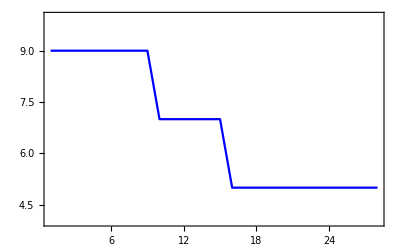

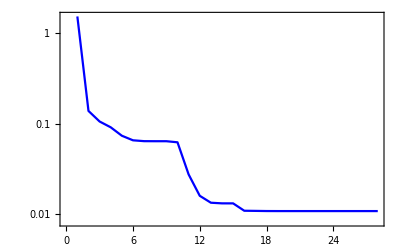

```mathematica
(*Plot sparsity and error convergence curve*)
Fig2b=ListLinePlot[g1,PlotRange->{All,{4,10}},Frame->True,PlotStyle->Blue]
Fig2c=ListLogPlot[g2,Joined->True,Frame->True,PlotStyle->Blue]
```

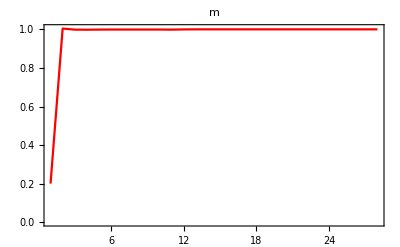
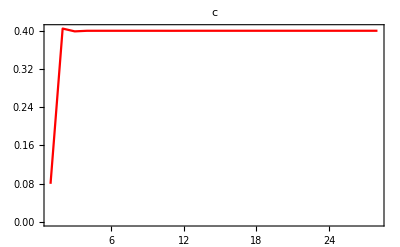
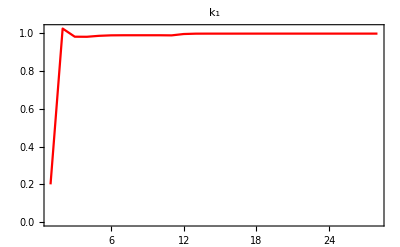
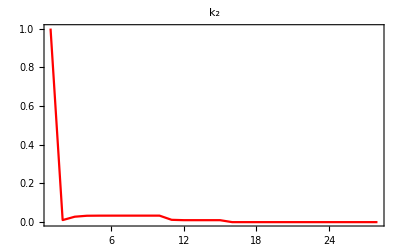
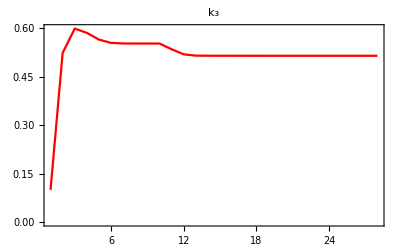
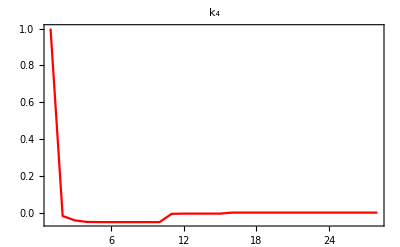
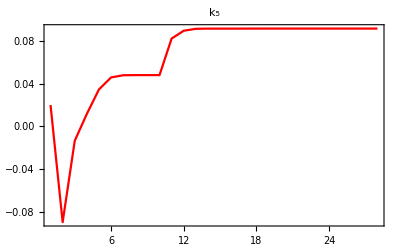
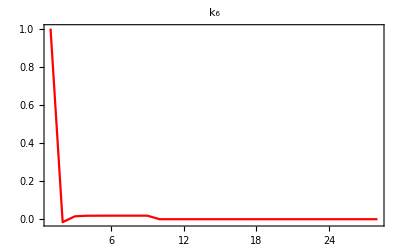

```mathematica
(*Plot iterative convergence curve for each physical parameter m,c,k1~k7*)
plotlabel={"m","c","k_1","k_2","k_3","k_4","k_5","k_6","k_7"};
Fig3=Table[ListLinePlot[Table[Xi[[1]][[j1]][[j2]],{j1,1,Length[Xi[[1]]]}],PlotStyle->Red,PlotRange->All,PlotLabel->plotlabel[[j2]],Frame->True],{j2,1,9}]
```

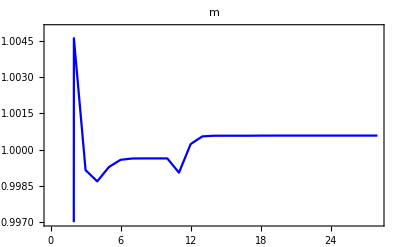
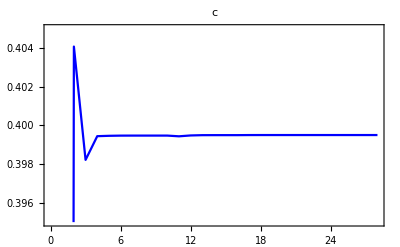
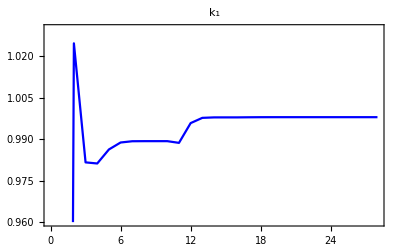
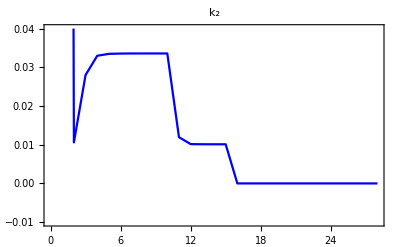
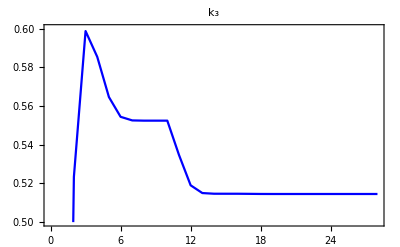
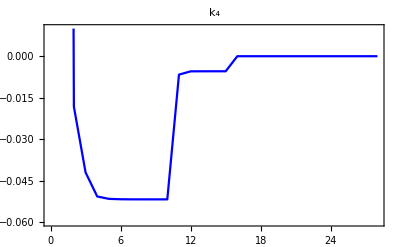
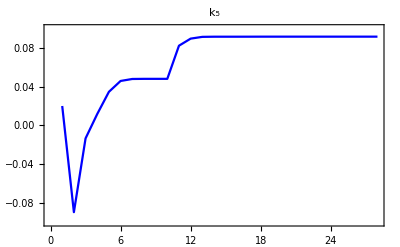
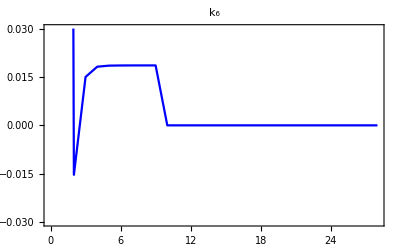

```mathematica
(*Custom vertical axis range for clearer visualization*)
YRange={{0.997,1.005},{0.395,0.405},{0.96,1.03},{-0.01,0.04},{0.5,0.6},{-0.06,0.01},{-0.1,0.1},{-0.03,0.03},{-0.01,0.1}};
Fig3Local=Table[ListLinePlot[Table[Xi[[1]][[j1]][[j2]],{j1,1,Length[Xi[[1]]]}],PlotStyle->Blue,PlotRange->YRange[[j2]],PlotLabel->plotlabel[[j2]],Frame->True],{j2,1,9}]
```